```mathematica
RK23[du_, u0_, t0_, T_,h_, tol_]:=Module[
{hcurr,tcurr,errcurr, k1,k2,k3,y ,i,ycurr},
hcurr = h;
tcurr = t0;

y = {{tcurr, u0}};
i =1;

While[ tcurr<T,

k1 = hcurr*du[tcurr, y[[i,2]]];
k2 = hcurr*du[tcurr +hcurr, y[[i,2]] + k1];
k3 = hcurr*du[tcurr +1/2 hcurr, y[[i,2]] + 1/4 k1+1/4 k2];

errcurr =Abs[-1/3(k1+k2-2k3)] ;

While[errcurr>tol,

hcurr = hcurr*(tol/errcurr)^(1/3);

k1 = hcurr*du[tcurr, y[[i,2]]];
k2 = hcurr*du[tcurr +hcurr, y[[i,2]] + k1];
k3 = hcurr*du[tcurr +1/2 hcurr, y[[i,2]] + 1/4 k1+1/4 k2];

errcurr =Abs[-1/3(k1+k2-2k3)] ;
];

hcurr = hcurr*(tol/errcurr)^(1/3);
k1 = hcurr*du[tcurr, y[[i,2]]];
k2 = hcurr*du[tcurr +hcurr, y[[i,2]] + k1];
k3 = hcurr*du[tcurr +1/2 hcurr, y[[i,2]] + 1/4 k1+1/4 k2];

AppendTo[y, {tcurr+hcurr, y[[i,2]]+1/6 k1+1/6 k2+2/3 k3//N}];
i++;
tcurr  =tcurr+hcurr;
];

Return[y];
]
```

```mathematica
b[t_]:=Piecewise[{{1, 0≤t<=2}, {3, t>2}}]
r[t_,u_]:=-b[t]*u+t;
a[t_]:=Piecewise[{{t-1+2 E^-t, 0≤t≤2}, {1/3 t-1/9+E^(-3t)(4/9 E^6+2 E^4), t>2}}]
```

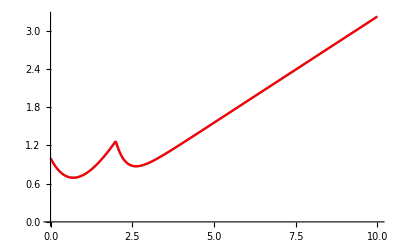

```mathematica
Show[{
ListLinePlot[RK23[r, 1,0,10,10, 0.0001],PlotRange->All],
Plot[a[t],{t,0,10},PlotStyle->Red]
}]
```